```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,3000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,0.0001,t,0],μ=RandomInteger[{1,14}]},ReplacePart[κ,{{μ,μ}}->ω+ⅈ*0.0001-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,0.0001,t,0],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{8,14}]},ReplacePart[κ,{{μ2,μ2},{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,0.0001,t,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]
```

```mathematica
tra[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1]},list={RandomSample[{imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1]}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];b]
```

```mathematica
Table[{ω,tra[ω,0.0001,1,0,0]},{ω,Range[0,3,0.001]}]
```

{{0.,1.12086×10^-6[0.,0.0001,1,0,0]},{0.001,1.09816×10^-6[0.001,0.0001,1,0,0]},{0.002,1.80399×10^-8[0.002,0.0001,1,0,0]},2995,{2.998,4.11193×10^-7[2.998,0.0001,1,0,0]},{2.999,1.61536×10^-7[2.999,0.0001,1,0,0]},{3.,0.000408528[3.,0.0001,1,0,0]}}
 |  |  |  |

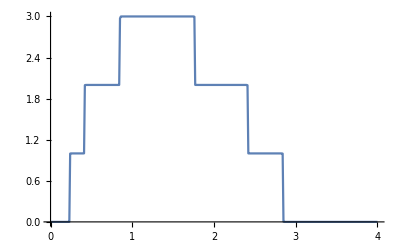

```mathematica
ListPlot[%18,Joined->True]
```

```mathematica
set[a1_,a2_]:=RandomChoice[Join[Table[imp1[ω,δ,t,ϵ,ϵ1],a1],Table[imp2[ω,δ,t,ϵ,ϵ1],a2],Table[imp[ω,δ,t,ϵ,ϵ1],100-a1-a2]],100]
```

```mathematica
Clear[imp1,imp2,set]
```

```mathematica
set[42,0]
```

{imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1],imp1[ω,δ,t,ϵ,ϵ1],imp[ω,δ,t,ϵ,ϵ1]}

```mathematica
misfit[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},lista={RandomSample[{imp9,imp2,imp,imp14,imp,imp,imp7,imp1,imp12,imp,imp,imp,imp,imp,imp,imp,imp,imp12,imp,imp4,imp11,imp11,imp,imp10,imp,imp,imp,imp,imp,imp7,imp,imp,imp,imp,imp,imp,imp12,imp7,imp14,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp12,imp10,imp6,imp4,imp,imp,imp10,imp14,imp10,imp,imp,imp,imp,imp4,imp8,imp10,imp14,imp1,imp14,imp,imp,imp,imp,imp14,imp2,imp,imp,imp14,imp,imp2,imp9,imp,imp,imp,imp10,imp,imp5,imp,imp8,imp7,imp,imp,imp3,imp,imp11,imp10,imp,imp,imp11}]};b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
m5=Table[{ω,tra},{ω,Range[0,4,0.01]}];
υ=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/140imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
list:={{1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10},{10,ρ11}};
{Min[list],list[[Position[list,Min[list]][[1,1]],1]],list}];
υ]
```

```mathematica
StandardDeviation[Table[%35[[x]][[1]],{x,100}]]
```

0.00019685

```mathematica
26
```

```mathematica
StandardDeviation[Table[misfit[0.5,1.5,1.49][[1]],500]]
```

0.00103477

```mathematica
Table[{x-0.85,StandardDeviation[Table[misfit[0.5,1.5,x][[1]],500]]},{x,Range[0.86,1.49,0.01]}]
```

{{0.01,0.00037752},{0.02,0.000295997},{0.03,0.000276242},{0.04,0.000263918},{0.05,0.000273155},{0.06,0.0002619},{0.07,0.000276494},{0.08,0.000264128},{0.09,0.000263968},{0.1,0.000249583},{0.11,0.000264194},{0.12,0.000249703},{0.13,0.000257694},{0.14,0.000267644},{0.15,0.000250826},{0.16,0.000263141},{0.17,0.000250309},{0.18,0.000262062},{0.19,0.000247184},{0.2,0.000271536},{0.21,0.000258256},{0.22,0.000281761},{0.23,0.000271323},{0.24,0.000275904},{0.25,0.00029912},{0.26,0.000283365},{0.27,0.000278507},{0.28,0.00030861},{0.29,0.000322797},{0.3,0.000321782},{0.31,0.000315436},{0.32,0.000321116},{0.33,0.000334226},{0.34,0.000354668},{0.35,0.000335074},{0.36,0.00033233},{0.37,0.000346747},{0.38,0.00035355},{0.39,0.000356578},{0.4,0.00036213},{0.41,0.000369071},{0.42,0.000381109},{0.43,0.000390046},{0.44,0.000393204},{0.45,0.000398068},{0.46,0.000427403},{0.47,0.000410968},{0.48,0.000430824},{0.49,0.000447978},{0.5,0.000476128},{0.51,0.000490641},{0.52,0.000474787},{0.53,0.000518929},{0.54,0.000551959},{0.55,0.00058241},{0.56,0.000622662},{0.57,0.000614619},{0.58,0.000675503},{0.59,0.000720564},{0.6,0.000783979},{0.61,0.000779719},{0.62,0.000924768},{0.63,0.000847237},{0.64,0.00104909}}

```mathematica
Transpose[%49]
```

{{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64},{0.00037752,0.000295997,0.000276242,0.000263918,0.000273155,0.0002619,0.000276494,0.000264128,0.000263968,0.000249583,0.000264194,0.000249703,0.000257694,0.000267644,0.000250826,0.000263141,0.000250309,0.000262062,0.000247184,0.000271536,0.000258256,0.000281761,0.000271323,0.000275904,0.00029912,0.000283365,0.000278507,0.00030861,0.000322797,0.000321782,0.000315436,0.000321116,0.000334226,0.000354668,0.000335074,0.00033233,0.000346747,0.00035355,0.000356578,0.00036213,0.000369071,0.000381109,0.000390046,0.000393204,0.000398068,0.000427403,0.000410968,0.000430824,0.000447978,0.000476128,0.000490641,0.000474787,0.000518929,0.000551959,0.00058241,0.000622662,0.000614619,0.000675503,0.000720564,0.000783979,0.000779719,0.000924768,0.000847237,0.00104909}}

```mathematica
%53[[2]]
```

{0.00037752,0.000295997,0.000276242,0.000263918,0.000273155,0.0002619,0.000276494,0.000264128,0.000263968,0.000249583,0.000264194,0.000249703,0.000257694,0.000267644,0.000250826,0.000263141,0.000250309,0.000262062,0.000247184,0.000271536,0.000258256,0.000281761,0.000271323,0.000275904,0.00029912,0.000283365,0.000278507,0.00030861,0.000322797,0.000321782,0.000315436,0.000321116,0.000334226,0.000354668,0.000335074,0.00033233,0.000346747,0.00035355,0.000356578,0.00036213,0.000369071,0.000381109,0.000390046,0.000393204,0.000398068,0.000427403,0.000410968,0.000430824,0.000447978,0.000476128,0.000490641,0.000474787,0.000518929,0.000551959,0.00058241,0.000622662,0.000614619,0.000675503,0.000720564,0.000783979,0.000779719,0.000924768,0.000847237,0.00104909}

```mathematica
Reverse[%54]
```

{0.00104909,0.000847237,0.000924768,0.000779719,0.000783979,0.000720564,0.000675503,0.000614619,0.000622662,0.00058241,0.000551959,0.000518929,0.000474787,0.000490641,0.000476128,0.000447978,0.000430824,0.000410968,0.000427403,0.000398068,0.000393204,0.000390046,0.000381109,0.000369071,0.00036213,0.000356578,0.00035355,0.000346747,0.00033233,0.000335074,0.000354668,0.000334226,0.000321116,0.000315436,0.000321782,0.000322797,0.00030861,0.000278507,0.000283365,0.00029912,0.000275904,0.000271323,0.000281761,0.000258256,0.000271536,0.000247184,0.000262062,0.000250309,0.000263141,0.000250826,0.000267644,0.000257694,0.000249703,0.000264194,0.000249583,0.000263968,0.000264128,0.000276494,0.0002619,0.000273155,0.000263918,0.000276242,0.000295997,0.00037752}

```mathematica
Range[0.01,0.64,0.01]
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64}

```mathematica
Join[%57,%55]
```

{0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.00104909,0.000847237,0.000924768,0.000779719,0.000783979,0.000720564,0.000675503,0.000614619,0.000622662,0.00058241,0.000551959,0.000518929,0.000474787,0.000490641,0.000476128,0.000447978,0.000430824,0.000410968,0.000427403,0.000398068,0.000393204,0.000390046,0.000381109,0.000369071,0.00036213,0.000356578,0.00035355,0.000346747,0.00033233,0.000335074,0.000354668,0.000334226,0.000321116,0.000315436,0.000321782,0.000322797,0.00030861,0.000278507,0.000283365,0.00029912,0.000275904,0.000271323,0.000281761,0.000258256,0.000271536,0.000247184,0.000262062,0.000250309,0.000263141,0.000250826,0.000267644,0.000257694,0.000249703,0.000264194,0.000249583,0.000263968,0.000264128,0.000276494,0.0002619,0.000273155,0.000263918,0.000276242,0.000295997,0.00037752}

```mathematica
{%63,%55}
```

{{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64},{0.00104909,0.000847237,0.000924768,0.000779719,0.000783979,0.000720564,0.000675503,0.000614619,0.000622662,0.00058241,0.000551959,0.000518929,0.000474787,0.000490641,0.000476128,0.000447978,0.000430824,0.000410968,0.000427403,0.000398068,0.000393204,0.000390046,0.000381109,0.000369071,0.00036213,0.000356578,0.00035355,0.000346747,0.00033233,0.000335074,0.000354668,0.000334226,0.000321116,0.000315436,0.000321782,0.000322797,0.00030861,0.000278507,0.000283365,0.00029912,0.000275904,0.000271323,0.000281761,0.000258256,0.000271536,0.000247184,0.000262062,0.000250309,0.000263141,0.000250826,0.000267644,0.000257694,0.000249703,0.000264194,0.000249583,0.000263968,0.000264128,0.000276494,0.0002619,0.000273155,0.000263918,0.000276242,0.000295997,0.00037752}}

```mathematica
Transpose[%64]
```

```mathematica
Join[{{0.001,0.5}},%67]
```

{{0.001,0.5},{0.01,0.00104909},{0.02,0.000847237},{0.03,0.000924768},{0.04,0.000779719},{0.05,0.000783979},{0.06,0.000720564},{0.07,0.000675503},{0.08,0.000614619},{0.09,0.000622662},{0.1,0.00058241},{0.11,0.000551959},{0.12,0.000518929},{0.13,0.000474787},{0.14,0.000490641},{0.15,0.000476128},{0.16,0.000447978},{0.17,0.000430824},{0.18,0.000410968},{0.19,0.000427403},{0.2,0.000398068},{0.21,0.000393204},{0.22,0.000390046},{0.23,0.000381109},{0.24,0.000369071},{0.25,0.00036213},{0.26,0.000356578},{0.27,0.00035355},{0.28,0.000346747},{0.29,0.00033233},{0.3,0.000335074},{0.31,0.000354668},{0.32,0.000334226},{0.33,0.000321116},{0.34,0.000315436},{0.35,0.000321782},{0.36,0.000322797},{0.37,0.00030861},{0.38,0.000278507},{0.39,0.000283365},{0.4,0.00029912},{0.41,0.000275904},{0.42,0.000271323},{0.43,0.000281761},{0.44,0.000258256},{0.45,0.000271536},{0.46,0.000247184},{0.47,0.000262062},{0.48,0.000250309},{0.49,0.000263141},{0.5,0.000250826},{0.51,0.000267644},{0.52,0.000257694},{0.53,0.000249703},{0.54,0.000264194},{0.55,0.000249583},{0.56,0.000263968},{0.57,0.000264128},{0.58,0.000276494},{0.59,0.0002619},{0.6,0.000273155},{0.61,0.000263918},{0.62,0.000276242},{0.63,0.000295997},{0.64,0.00027752}}

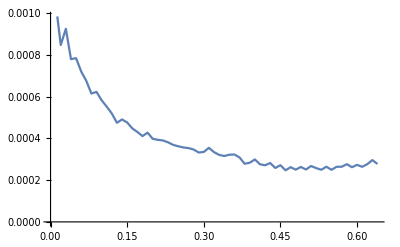

```mathematica
ListPlot[%70,Joined->True]
```

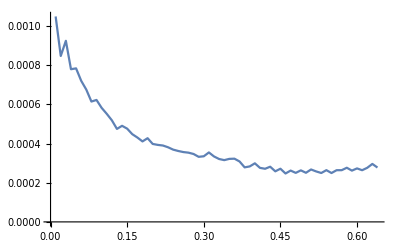

```mathematica
ListPlot[%67,Joined->True]
```

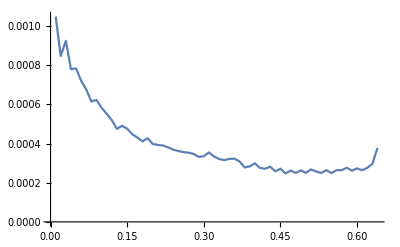

```mathematica
ListPlot[%65,Joined->True]
```

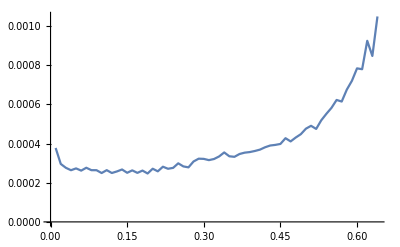

```mathematica
ListPlot[%49,Joined->True,PlotRange->All]
```

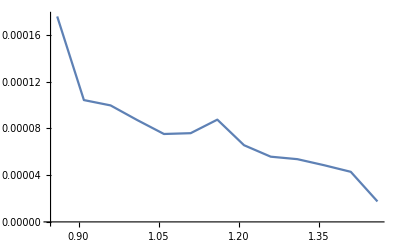

```mathematica
ListPlot[%43,Joined->True]
```

```mathematica
Table[misfit[0.5,1.5,0.85],100]
```

$Aborted